```mathematica
(*Global variables definitions*)

V[x_]= x^2;
ℏ = 1;
m =0.51099892;
```

{{f→InterpolatingFunction[{{-100.,100.}},<>]}}

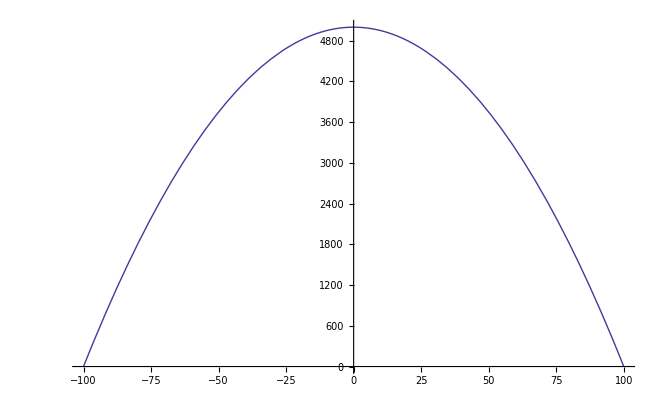

```mathematica
NDSolve[{-f''[x]==1,f[100]==0,f[-100] == 0},f,{x,-100,100}]
Plot[First[f[x]/.%],{x,-100,100}]
```

```mathematica
(*Define a Hamiltonian*)
```

```mathematica
V[x_] = x^2;
H[ψ_]=-ℏ^2/(2m)Dt[ψ,{x,2}] + V [x]* ψ
```

x^2 ψ-0.978476 Dt[ψ,{x,2}]

```mathematica
(*Solve schrodinger eqn Ĥ ψ = Eψ*)
```

```mathematica
sol = DSolve[H[Ψ[x]] == Energy[λ] * Ψ[x],Ψ[x],x]
```

{{Ψ[x]→C[2] ParabolicCylinderD[-0.5-0.50547 Energy[λ],(0.+1.42193 ⅈ) x]+C[1] ParabolicCylinderD[-0.5+0.50547 Energy[λ],1.42193 x]}}

```mathematica
(*Taking only the real solutions*)
```

```mathematica
hermitialSolution = FunctionExpand[Ψ[x] /. sol]/.C[2]-> 0
```

{2^(1/2 (0.5-0.50547 Energy[λ])) ⅇ^(-0.50547 x^2) C[1] HermiteH[-0.5+0.50547 Energy[λ],1.00545 x]}

```mathematica
(*obtain allowed energies*)
```

```mathematica
En[λ_] = Solve[(-ℏ+√2 √m Energy[λ])/(2 ℏ)==λ,Energy[λ]]
```

{{Energy[λ]→1.97836 (0.5+1. λ)}}

```mathematica
(*Eigenvalues*)
```

```mathematica
evals= Table[Energy[λ] /.En[λ],{λ,0,10}]//Flatten
```

{0.989179,2.96754,4.9459,6.92425,8.90261,10.881,12.8593,14.8377,16.816,18.7944,20.7728}

```mathematica
(*Eigenfunctions*)
```

```mathematica
psi[λ_,x_] = First@(hermitialSolution/.C[1]->Normalize[psi[0,x]]/.En[λ]/.m->.510/.ℏ->1//Flatten)
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

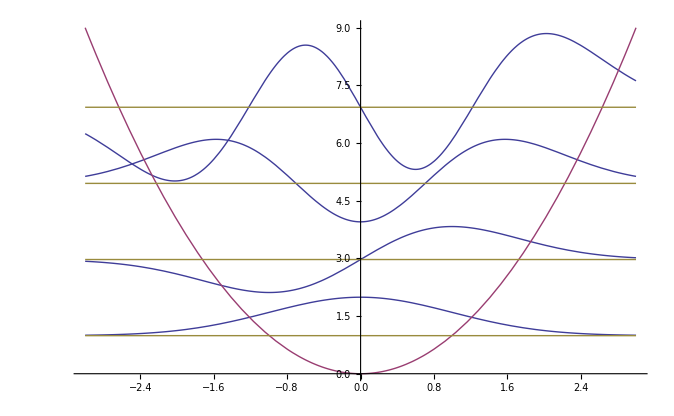

```mathematica
Plot[
{Evaluate[Table[psi[n,x]+ evals[[n+1]],{n,0,3}]/.m-> .510/.ℏ->1],x^2,Table[evals[[n]]/.m->.510/.ℏ->1,{n,1,4}]},{x,-3,3},PlotRange->All]
```

```mathematica
(*******************************************************************************************************)
Clear["Global`*"]
```

We wish to solve the follwing Equations Selfconsistently-ℏ^2/2 d/dx(1/(m^*(x))d/dx)ψ(x) + V(x)ψ(x) = Eψ(x)(1)
d/dx(ϵ_s(x)d/dx)ϕ(x) = (-q[N_D(x) - n(x)])/ϵ_0(2)
V(x)=-qϕ(x)+ΔE_c(x)(3)
n(x)=(Σ_(k=1))^m(ψ^*)_k(x) ψ_k(x) n_k  (4)
n_k= m^*/(π ℏ^2)∫_E_k^∞ 1/(1+e^((E-E_F)/kT))ⅆE   (5)

```mathematica
(*Trial V[x]*)
```

```mathematica
V[x_] = x;
```

```mathematica
(*Define a Hamiltonian and solve Schrodinger for particular V[x],*)
```

```mathematica
H[ψ_]=-ℏ^2/(2m)Dt[ψ,{x,2}] + V [x]* ψ;
solSch = DSolve[H[ψ[x]] == Energy[λ] * ψ[x],ψ[x],x]
```

{{ψ[x]→AiryAi[((2 m x)/ℏ^2-(2 m Energy[λ])/ℏ^2)/(2^(2/3) (m/ℏ^2)^(2/3))] C[1]+AiryBi[((2 m x)/ℏ^2-(2 m Energy[λ])/ℏ^2)/(2^(2/3) (m/ℏ^2)^(2/3))] C[2]}}

```mathematica
(*discretize*)
```

```mathematica
En[λ_]=Solve[(-(2 m Energy[λ])/ℏ^2)/(2^(2/3) (m/ℏ^2)^(2/3))==λ,Energy[λ]]
```

{{Energy[λ]→-(λ (m/ℏ^2)^(2/3) ℏ^2)/(2^(1/3) m)}}

```mathematica
evals= Table[Energy[λ] /.En[λ],{λ,0,5}]//Flatten
```

{0,-((m/ℏ^2)^(2/3) ℏ^2)/(2^(1/3) m),-(2^(2/3) (m/ℏ^2)^(2/3) ℏ^2)/m,-(3 (m/ℏ^2)^(2/3) ℏ^2)/(2^(1/3) m),-(2 2^(2/3) (m/ℏ^2)^(2/3) ℏ^2)/m,-(5 (m/ℏ^2)^(2/3) ℏ^2)/(2^(1/3) m)}

```mathematica
(*Eigenfunction*)
psi[λ_,x_] = First@(ψ[x]/.solSch/.C[1]->1(*Normalize[psi[0,x]]*)/.C[2]->0(*Normalize[psi[0,x]]*)/.En[λ]/.m->.510/.ℏ->1//Flatten)
```

AiryAi[0.986885 (1.02 x+1.01329 λ)]

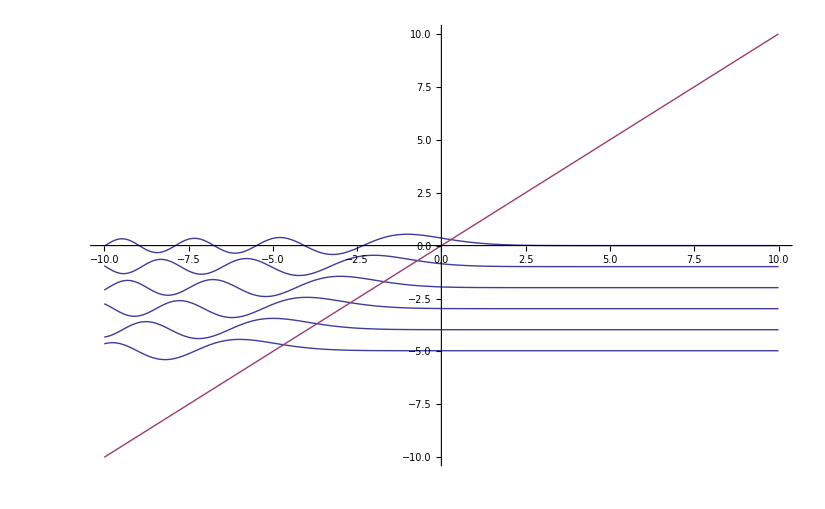

```mathematica
Plot[{Table[psi[n,x]+(evals[[n+1]]/.ℏ-> 1/.m-> .510 ),{n,0,5}],x},{x,-10,10}]
```

```mathematica
(*now that we have our eigenfunctions ψk, we can find the electron density*)
```

```mathematica
nk =Table[ m/(π ℏ^2)∫_evals[[k]]^∞ 1/(1+Exp[e - Ef])ⅆe,{k,1,3}]
```

{(m Log[1+ⅇ^Ef])/(π ℏ^2),(m (1/(2^(1/3) (m/ℏ^2)^(1/3))+Log[ⅇ^Ef+ⅇ^(-1/(2^(1/3) (m/ℏ^2)^(1/3)))]))/(π ℏ^2),(m (2^(2/3)/((m/ℏ^2)^(1/3))+Log[ⅇ^Ef+ⅇ^(-2^(2/3)/((m/ℏ^2)^(1/3)))]))/(π ℏ^2)}

```mathematica
n[x_] = Sum[Abs[psi[k,x]]^2 nk[[k]],{k,1,3}]
```

(m Abs[AiryAi[0.986885 (1.01329+1.02 x)]]^2 Log[1+ⅇ^Ef])/(π ℏ^2)+(m Abs[AiryAi[0.986885 (2.02658+1.02 x)]]^2 (1/(2^(1/3) (m/ℏ^2)^(1/3))+Log[ⅇ^Ef+ⅇ^(-1/(2^(1/3) (m/ℏ^2)^(1/3)))]))/(π ℏ^2)+(m Abs[AiryAi[0.986885 (3.03987+1.02 x)]]^2 (2^(2/3)/((m/ℏ^2)^(1/3))+Log[ⅇ^Ef+ⅇ^(-2^(2/3)/((m/ℏ^2)^(1/3)))]))/(π ℏ^2)

```mathematica
(*plugging that into poisson's eqn*)
```

```mathematica
solPoi = DSolve[Dt[ϕ[x],{x,2}] == -q/(ϵs ϵ0)(Nd - n[x]),ϕ[x],x]
```

{{ϕ[x]→C[1]+x C[2]+∫_1^x (∫_1^K[2] -1/(ϵ0 ϵs (m/ℏ^2)^(1/3) ℏ^2)0.159155 (6.28319 Nd q (m/ℏ^2)^(1/3) ℏ^2-1.5874 m q Abs[AiryAi[0.986885 (2.02658+1.02 K[1])]]^2-3.1748 m q Abs[AiryAi[0.986885 (3.03987+1.02 K[1])]]^2-2. m q (m/ℏ^2)^(1/3) Abs[AiryAi[0.986885 (1.01329+1.02 K[1])]]^2 Log[1.+ⅇ^Ef]-2. m q (m/ℏ^2)^(1/3) Abs[AiryAi[0.986885 (3.03987+1.02 K[1])]]^2 Log[ⅇ^Ef+ⅇ^(-1.5874/((m/ℏ^2)^(1/3)))]-2. m q (m/ℏ^2)^(1/3) Abs[AiryAi[0.986885 (2.02658+1.02 K[1])]]^2 Log[ⅇ^Ef+ⅇ^(-0.793701/((m/ℏ^2)^(1/3)))])ⅆK[1])ⅆK[2]}}

```mathematica
(*now, the new potential is given by:*)
Vn[x_] = First@(-q*(ϕ[x]/.solPoi)+Ec)
```

Ec-q (C[1]+x C[2]+∫_1^x (∫_1^K[2] -1/(ϵ0 ϵs (m/ℏ^2)^(1/3) ℏ^2)0.159155 (6.28319 Nd q (m/ℏ^2)^(1/3) ℏ^2-1.5874 m q Abs[AiryAi[0.986885 (2.02658+1.02 K[1])]]^2-3.1748 m q Abs[AiryAi[0.986885 (3.03987+1.02 K[1])]]^2-2. m q (m/ℏ^2)^(1/3) Abs[AiryAi[0.986885 (1.01329+1.02 K[1])]]^2 Log[1.+ⅇ^Ef]-2. m q (m/ℏ^2)^(1/3) Abs[AiryAi[0.986885 (3.03987+1.02 K[1])]]^2 Log[ⅇ^Ef+ⅇ^(-1.5874/((m/ℏ^2)^(1/3)))]-2. m q (m/ℏ^2)^(1/3) Abs[AiryAi[0.986885 (2.02658+1.02 K[1])]]^2 Log[ⅇ^Ef+ⅇ^(-0.793701/((m/ℏ^2)^(1/3)))])ⅆK[1])ⅆK[2])

```mathematica
Vn[x]/.C[1]->1/.C[2]->2/.Ec->1/.Ef->π/.ℏ->1/.m->.510
```

1-q (1+2 x+∫_1^x (∫_1^K[2] -1/(ϵ0 ϵs)0.199203 (5.01999 Nd q-2.59467 q Abs[AiryAi[0.986885 (1.01329+1.02 K[1])]]^2-3.38271 q Abs[AiryAi[0.986885 (2.02658+1.02 K[1])]]^2-4.18416 q Abs[AiryAi[0.986885 (3.03987+1.02 K[1])]]^2)ⅆK[1])ⅆK[2])